### Autonomous Equations :

```mathematica
Eqx = 3/2 x[η](-1+x[η]^2-y[η]^2)+√(3/2) y[η]^2 λ;
Eqy=  -1/2 y[η](-3-3 x[η]^2+3 y[η]^2+√6 x[η] λ);
```

```mathematica
ex=Eqx/.x_[η]->x
ey=Eqy/.x_[η]->x
```

3/2 x (-1+x^2-y^2)+√(3/2) y^2 λ

-1/2 y (-3-3 x^2+3 y^2+√6 x λ)

### Cosmological parameters in terms of dimensionless variables :

```mathematica
Ωphi=x^2+y^2;
Ωm=1-Ωphi;
wphi=(x^2-y^2)/(x^2+y^2);
weff=Ωphi*wphi + Ωm *w ;
w=0;
λ=1;
```

### Phase Space Boundary : Ωm ≥ 0 => (x^2 + y^2 ≤ 1)

```mathematica
boundsf=RegionPlot[x^2+y^2<1&&y>0,{x,-1,1},{y,0,1},PlotStyle->None,BoundaryStyle->Thickness[0.003]];
```

### Critical points:

```mathematica
cp=Graphics[{PointSize[0.02],Point[{0,0}], Point [{1,0}], Point[{-1,0}],Red,Point[{λ/(√6),√((6-λ^2)/6)}]}];
```

```mathematica
Heteroclinic orbit
```

```mathematica
nsol=NDSolve[Evaluate[{{Eqx==x'[η],Eqy==y'[η]}, x[0]==0,y[0]==0.01}], {x[η], y[η]}, {η, 0, 100},MaxSteps->10^5,StartingStepSize->0.001,MaxStepFraction->1/1000]
```

{{x[η]→InterpolatingFunction[…][η],y[η]→InterpolatingFunction[…][η]}}

### Parametric Plot

```mathematica
pt=ParametricPlot[Evaluate[
{Re[x[η]],Re[y[η]]}/.nsol[[1]]],
 {η,0, 100},PlotPoints -> 200,PlotStyle->{Red,Thick,Dashed}];
```

#### Point labels:

```mathematica
labelsf=Graphics[{Text[Style["A",40],{0,0},{-1,-1}], Text[Style["B",40],{λ/(√6),(√(6-λ^2))/(√6)},{-1,-1}] }];
```

### Accelerated region

```mathematica
acc=RegionPlot[x^2-y^2≤-1/3&&y>0&&-1<weff<-1/3 &&x^2+y^2<=1,{x,-5,5},{y,0,4},PlotPoints->50, PlotStyle->Opacity[0.30,Yellow],BoundaryStyle->None,Frame->True,Axes->False,FrameLabel->{X,Y},FrameStyle->30,RotateLabel->False,AspectRatio->1/2,ImageSize->1000];
```

Stream Plot:

```mathematica
st=StreamPlot[{ex,ey},{x,-1,1},{y,0,1},RegionFunction->Function[{X,Y},Y^2+X^2<1&&Y>0],AspectRatio->1/2,ImageSize->1000,Frame->True,Axes->False,FrameLabel->{x,y},FrameStyle->30,FrameTicksStyle->Directive[Black,FontSize->16],LabelStyle->{FontSize->10},RotateLabel->False];
```

#### Display

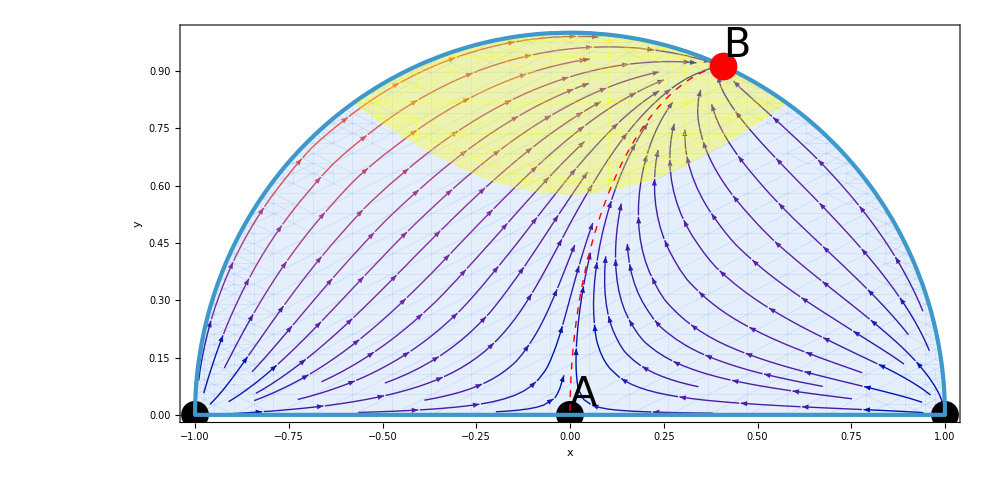

```mathematica
Show[st,acc,pt,boundsf,cp,labelsf]
```

```mathematica
Anil= Show[st,acc,pt,boundsf,cp,labelsf]
```

-Graphics-

```mathematica
Export["~/Desktop/Quintessencefinal.pdf",Rasterize[Anil,ImageResolution->300]]  (* Rasterize is for no cracks on image while exporting image*)
```

~/Desktop/Quintessencefinal.pdf

### Let’s see what it actually means

```mathematica
Canvas[%]
```

-Graphics-~/Desktop/Quintessencefinal.pdf

### For λ = 1 , Universe goes to accelerating region . Matter density is diluting and Scalar field is dominating . For λ = 2, Cannot drive acceleration. Scalar field domination (Decelerated expansion). You can see it by substituting in this code. For λ = 2, Quintessence-dominated point does not exist.